### In this notebook, we will see if the BDF2OPT formula will give us the variable step size BDFL3 method

```mathematica
bdf2a=({0,Subscript[ω, n]^2/(1+2 Subscript[ω, n]),-(1+Subscript[ω, n])^2/(1+2 Subscript[ω, n]),1}/((1+Subscript[ω, n])/(1+2 Subscript[ω, n]))); (*Subscript[α, 0],Subscript[α, 1],Subscript[α, 2],Subscript[α, 3]*)
bdf2b={0,0,0,1}; 
bdf3a={-(Subscript[ω, n]^3 Subscript[ω, 1+n] (1+Subscript[ω, 1+n]))/((1+Subscript[ω, n]) (1+Subscript[ω, n] (1+Subscript[ω, 1+n]))),Subscript[ω, 1+n] (Subscript[ω, n]+1/(1+Subscript[ω, 1+n])),-((1+Subscript[ω, 1+n]) (1+Subscript[ω, n] (1+Subscript[ω, 1+n])))/((1+Subscript[ω, n]) Subscript[ω, 1+n]),(1+2 Subscript[ω, 1+n]+Subscript[ω, n] (1+4 Subscript[ω, 1+n]+3 Subscript[ω, 1+n]^2))/(Subscript[ω, 1+n] (1+Subscript[ω, 1+n]) (1+Subscript[ω, n] (1+Subscript[ω, 1+n])))};
bdf3b={0,0,0,1};
bdfopta[β_]:=β bdf3a+(1-β)bdf2a;
bdfoptb[β_]:=β bdf3b+(1-β)bdf2b;
```

```mathematica
bdf2a//Simplify
```

{0,ω_n^2/(1+ω_n),-1-ω_n,(1+2 ω_n)/(1+ω_n)}

#### Double checking coefficients

```mathematica
bdf2a/.{Subscript[ω, n]->1}
bdf3a/.{Subscript[ω, n]->1,Subscript[ω, n+1]->1}
```

{0,1/2,-2,3/2}

{-1/3,3/2,-3,11/6}

#### We now let β=1/2

```mathematica
bdfopta[1/2]//Simplify
```

{-(ω_n^3 ω_(1+n) (1+ω_(1+n)))/(2 (1+ω_n) (1+ω_n (1+ω_(1+n)))),1/2 (ω_n^2/(1+ω_n)+ω_(1+n) (ω_n+1/(1+ω_(1+n)))),1/2 (-1-ω_n-((1+ω_(1+n)) (1+ω_n (1+ω_(1+n))))/((1+ω_n) ω_(1+n))),1/2 ((1+2 ω_n)/(1+ω_n)+(1+2 ω_(1+n)+ω_n (1+4 ω_(1+n)+3 ω_(1+n)^2))/(ω_(1+n) (1+ω_(1+n)) (1+ω_n (1+ω_(1+n)))))}

#### Checking if they match BDFL3 coefficients

```mathematica
bdfopta[1/2]/.{Subscript[ω, n]->1,Subscript[ω, n+1]->1}
```

{-1/6,1,-5/2,5/3}

#### Note that if we normalize BDFL3 such that β_3=1, we get the same coefficients

```mathematica
{-1/10,3/5,3/2,1}*5/3
```

{-1/6,1,5/2,5/3}

#### Let’s now check consistency

```mathematica
ClearAll["`*"]
```

```mathematica
c[j_,k_]:=Sum[1/Product[Subscript[ω, n-l+k-2],{l,0,k-2-i}],{i,0,j-1}]
```

```mathematica
variablestepcond[p_,k_]:=Table[(Sum[Subscript[α, n,j] c[j,k]^(m+ε),{j,0,k}]==m Sum[Subscript[β, n,j] c[j,k]^(m-1+ε),{j,0,k}]),{m,0,p}]/. {0^ε->1,ε->0,0^(-1+ε)->0}
```

```mathematica
variablestepcond[2,3]/.{Subscript[β, n,3]->1,Subscript[β, n,0]->0,Subscript[β, n,1]->0,Subscript[β, n,2]->0}
```

{α_(n,0)+α_(n,1)+α_(n,2)+α_(n,3)==0,(α_(n,1))/(ω_n ω_(1+n))+(1/(ω_(1+n))+1/(ω_n ω_(1+n))) α_(n,2)+(1+1/(ω_(1+n))+1/(ω_n ω_(1+n))) α_(n,3)==1,(α_(n,1))/(ω_n^2 ω_(1+n)^2)+(1/(ω_(1+n))+1/(ω_n ω_(1+n)))^2 α_(n,2)+(1+1/(ω_(1+n))+1/(ω_n ω_(1+n)))^2 α_(n,3)==2 (1+1/(ω_(1+n))+1/(ω_n ω_(1+n)))}

#### 0-order (α_(n,0)+α_(n,1)+α_(n,2)+α_(n,3)==0)

```mathematica
Sum[bdfopta[1/2][[i]],{i,1,4}]//Simplify
```

0

#### 1-order ((α_(n,1))/(ω_n ω_(1+n))+(1/(ω_(1+n))+1/(ω_n ω_(1+n))) α_(n,2)+(1+1/(ω_(1+n))+1/(ω_n ω_(1+n))) α_(n,3)==1)

```mathematica
Subscript[α, n,1]/(Subscript[ω, n] Subscript[ω, 1+n])+(1/Subscript[ω, 1+n]+1/(Subscript[ω, n] Subscript[ω, 1+n])) Subscript[α, n,2]+(1+1/Subscript[ω, 1+n]+1/(Subscript[ω, n] Subscript[ω, 1+n])) Subscript[α, n,3]/.{Subscript[α, n,1]->bdfopta[1/2][[2]],Subscript[α, n,2]->bdfopta[1/2][[3]],Subscript[α, n,3]->bdfopta[1/2][[4]]}//FullSimplify
```

(1+ω_n-ω_n^2+(1+2 ω_n) ω_(1+n))/(2 (1+ω_n) ω_(1+n))

#### 2-order ((α_(n,1))/(ω_n^2 ω_(1+n)^2)+(1/(ω_(1+n))+1/(ω_n ω_(1+n)))^2 α_(n,2)+(1+1/(ω_(1+n))+1/(ω_n ω_(1+n)))^2 α_(n,3)==2 (1+1/(ω_(1+n))+1/(ω_n ω_(1+n))))

```mathematica
Subscript[α, n,1]/(Subscript[ω, n]^2 Subscript[ω, 1+n]^2)+(1/Subscript[ω, 1+n]+1/(Subscript[ω, n] Subscript[ω, 1+n]))^2 Subscript[α, n,2]+(1+1/Subscript[ω, 1+n]+1/(Subscript[ω, n] Subscript[ω, 1+n]))^2 Subscript[α, n,3]==2 (1+1/Subscript[ω, 1+n]+1/(Subscript[ω, n] Subscript[ω, 1+n]))/.{Subscript[α, n,1]->bdfopta[1/2][[2]],Subscript[α, n,2]->bdfopta[1/2][[3]],Subscript[α, n,3]->bdfopta[1/2][[4]]}//Simplify
```

(ω_n^3+2 (-1+ω_(1+n))+2 ω_n^2 (-1+ω_(1+n)) ω_(1+n)+ω_n (-4+3 ω_(1+n)^2))/(ω_n (1+ω_n) ω_(1+n))==0

#### Let’s assume that the method found above satisfies the consistency conditions and check for 0-stability

```mathematica
ρ[a_][xi_]:=Sum[a[[i+1]] xi^i,{i,0,Length[a]-1}]
σ[b_][xi_]:=Sum[b[[i+1]] xi^i,{i,0,Length[b]-1}]
```

```mathematica
alphas={-(Subscript[ω, n]^2 (1+Subscript[ω, n]) Subscript[ω, 1+n]^3)/(2 (1+Subscript[ω, 1+n]) (1+(1+Subscript[ω, n]) Subscript[ω, 1+n])),1/2 Subscript[ω, n]^2 (2/(1+Subscript[ω, n])+Subscript[ω, 1+n]),-((1+Subscript[ω, n]) (2+(2+Subscript[ω, n]) Subscript[ω, 1+n]))/(2 (1+Subscript[ω, 1+n])),1/2 (1+1/(1+Subscript[ω, n])+Subscript[ω, n] (3/(1+Subscript[ω, n])+Subscript[ω, 1+n]/(1+(1+Subscript[ω, n]) Subscript[ω, 1+n])))};
```

```mathematica
rho=ρ[alphas][ζ]
```

1/2 ζ ω_n^2 (2/(1+ω_n)+ω_(1+n))-(ω_n^2 (1+ω_n) ω_(1+n)^3)/(2 (1+ω_(1+n)) (1+(1+ω_n) ω_(1+n)))-(ζ^2 (1+ω_n) (2+(2+ω_n) ω_(1+n)))/(2 (1+ω_(1+n)))+1/2 ζ^3 (1+1/(1+ω_n)+ω_n (3/(1+ω_n)+(ω_(1+n))/(1+(1+ω_n) ω_(1+n))))

```mathematica
roots=(Abs[ζ/.Solve[rho==0,ζ]])//Simplify
```

{1,1/2 Abs[(2 ω_n^2+5 ω_n^2 ω_(1+n)+3 ω_n^3 ω_(1+n)+4 ω_n^2 ω_(1+n)^2+5 ω_n^3 ω_(1+n)^2+ω_n^4 ω_(1+n)^2-√(ω_n^4 (2+(5+3 ω_n) ω_(1+n)+(4+5 ω_n+ω_n^2) ω_(1+n)^2)^2-4 ω_n^2 (1+ω_n)^2 ω_(1+n)^3 (1+ω_(1+n)) (5 ω_n^2 ω_(1+n)+2 (1+ω_(1+n))+ω_n (4+7 ω_(1+n)))))/((1+ω_(1+n)) (5 ω_n^2 ω_(1+n)+2 (1+ω_(1+n))+ω_n (4+7 ω_(1+n))))],1/2 Abs[(2 ω_n^2+5 ω_n^2 ω_(1+n)+3 ω_n^3 ω_(1+n)+4 ω_n^2 ω_(1+n)^2+5 ω_n^3 ω_(1+n)^2+ω_n^4 ω_(1+n)^2+√(ω_n^4 (2+(5+3 ω_n) ω_(1+n)+(4+5 ω_n+ω_n^2) ω_(1+n)^2)^2-4 ω_n^2 (1+ω_n)^2 ω_(1+n)^3 (1+ω_(1+n)) (5 ω_n^2 ω_(1+n)+2 (1+ω_(1+n))+ω_n (4+7 ω_(1+n)))))/((1+ω_(1+n)) (5 ω_n^2 ω_(1+n)+2 (1+ω_(1+n))+ω_n (4+7 ω_(1+n))))]}

```mathematica
Reduce[roots[[2]]<1&&roots[[3]]<1&&Subscript[ω, n]∈Reals&&Subscript[ω, n+1]∈Reals,{Subscript[ω, n],Subscript[ω, n+1]}]
```

$Aborted

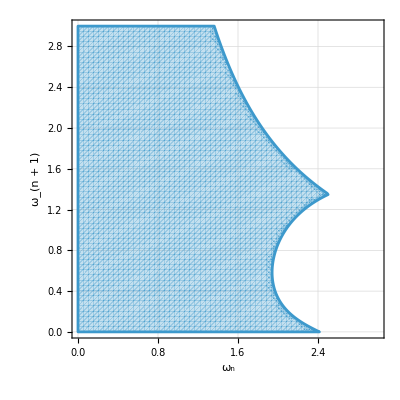

```mathematica
RegionPlot[roots[[2]]<1&&roots[[3]]<1,{Subscript[ω, n],0,3},{Subscript[ω, n+1],0,3},GridLines->Automatic,FrameLabel->{Subscript[ω, n], "ω_(n + 1)"},RotateLabel->False,PlotPoints->60]
```

#### This method is therefore 0-stable

```mathematica
βtest=bdfopta[β]
```

{-(β ω_n^3 ω_(1+n) (1+ω_(1+n)))/((1+ω_n) (1+ω_n (1+ω_(1+n)))),((1-β) ω_n^2)/(1+ω_n)+β ω_(1+n) (ω_n+1/(1+ω_(1+n))),(1-β) (-1-ω_n)-(β (1+ω_(1+n)) (1+ω_n (1+ω_(1+n))))/((1+ω_n) ω_(1+n)),((1-β) (1+2 ω_n))/(1+ω_n)+(β (1+2 ω_(1+n)+ω_n (1+4 ω_(1+n)+3 ω_(1+n)^2)))/(ω_(1+n) (1+ω_(1+n)) (1+ω_n (1+ω_(1+n))))}

```mathematica
alphacoeffsnorm={(Subscript[ω, n]^2 (-1-2 Subscript[ω, 1+n]+2 Subscript[ω, 1+n]^2))/(2+4 Subscript[ω, n] (1+Subscript[ω, 1+n])),(1+2 Subscript[ω, n] (1+Subscript[ω, 1+n])+Subscript[ω, n]^2 (1+2 Subscript[ω, 1+n]-2 Subscript[ω, 1+n]^2))/(2+4 Subscript[ω, n] (1+Subscript[ω, 1+n])),-3/2,1}/((-1+2 Subscript[ω, 1+n]+Subscript[ω, n] (-1+4 Subscript[ω, 1+n]+2 Subscript[ω, 1+n]^2))/(2 Subscript[ω, 1+n] (1+2 Subscript[ω, n] (1+Subscript[ω, 1+n]))))//FullSimplify
```

{(ω_n^2 ω_(1+n) (-1+2 (-1+ω_(1+n)) ω_(1+n)))/(-1+2 ω_(1+n)+ω_n (-1+2 ω_(1+n) (2+ω_(1+n)))),(ω_(1+n) (1+ω_n (2+ω_n+2 (1+ω_n) ω_(1+n)-2 ω_n ω_(1+n)^2)))/(-1+2 ω_(1+n)+ω_n (-1+2 ω_(1+n) (2+ω_(1+n)))),-(3 ω_(1+n) (1+2 ω_n (1+ω_(1+n))))/(-1+2 ω_(1+n)+ω_n (-1+2 ω_(1+n) (2+ω_(1+n)))),(2 ω_(1+n) (1+2 ω_n (1+ω_(1+n))))/(-1+2 ω_(1+n)+ω_n (-1+2 ω_(1+n) (2+ω_(1+n))))}

```mathematica
Sum[alphacoeffsnorm[[i]],{i,1,4}]==0//Simplify
```

True

```mathematica
Subscript[α, n,1]/(Subscript[ω, n] Subscript[ω, 1+n])+(1/Subscript[ω, 1+n]+1/(Subscript[ω, n] Subscript[ω, 1+n])) Subscript[α, n,2]+(1+1/Subscript[ω, 1+n]+1/(Subscript[ω, n] Subscript[ω, 1+n])) Subscript[α, n,3]==1/.{Subscript[α, n,1]->alphacoeffsnorm[[2]],Subscript[α, n,2]->alphacoeffsnorm[[3]],Subscript[α, n,3]->alphacoeffsnorm[[4]]}//FullSimplify
```

True

```mathematica
Subscript[α, n,1]/(Subscript[ω, n]^2 Subscript[ω, 1+n]^2)+(1/Subscript[ω, 1+n]+1/(Subscript[ω, n] Subscript[ω, 1+n]))^2 Subscript[α, n,2]+(1+1/Subscript[ω, 1+n]+1/(Subscript[ω, n] Subscript[ω, 1+n]))^2 Subscript[α, n,3]==2 (1+1/Subscript[ω, 1+n]+1/(Subscript[ω, n] Subscript[ω, 1+n]))/.{Subscript[α, n,1]->alphacoeffsnorm[[2]],Subscript[α, n,2]->alphacoeffsnorm[[3]],Subscript[α, n,3]->alphacoeffsnorm[[4]]}//Simplify
```

True

```mathematica
Solve[-(β Subscript[ω, n]^3 Subscript[ω, 1+n] (1+Subscript[ω, 1+n]))/((1+Subscript[ω, n]) (1+Subscript[ω, n] (1+Subscript[ω, 1+n])))==(Subscript[ω, n]^2 Subscript[ω, 1+n] (-1+2 (-1+Subscript[ω, 1+n]) Subscript[ω, 1+n]))/(-1+2 Subscript[ω, 1+n]+Subscript[ω, n] (-1+2 Subscript[ω, 1+n] (2+Subscript[ω, 1+n]))),β]//FullSimplify
```

{{β→-((1+ω_n) (-1+2 (-1+ω_(1+n)) ω_(1+n)) (1+ω_n (1+ω_(1+n))))/(ω_n (1+ω_(1+n)) (-1+2 ω_(1+n)+ω_n (-1+2 ω_(1+n) (2+ω_(1+n)))))}}

```mathematica
{{β->-((1+Subscript[ω, n]) (-1+2 (-1+Subscript[ω, 1+n]) Subscript[ω, 1+n]) (1+Subscript[ω, n] (1+Subscript[ω, 1+n])))/(Subscript[ω, n] (1+Subscript[ω, 1+n]) (-1+2 Subscript[ω, 1+n]+Subscript[ω, n] (-1+2 Subscript[ω, 1+n] (2+Subscript[ω, 1+n]))))}}/.{Subscript[ω, n]->1,Subscript[ω, n+1]->1}
```

{{β→1/2}}